NDSolve::precw: The precision of the differential equation (…) is less than WorkingPrecision (30.).

NDSolve::ndsz: At t == 1.65805571017885042618821729718, step size is effectively zero; singularity or stiff system suspected.

-Graphics3D-

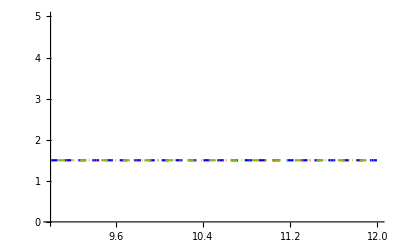

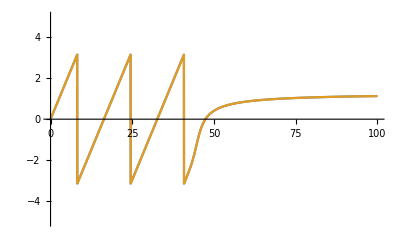

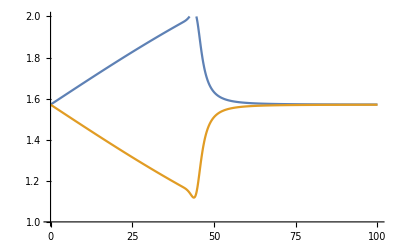

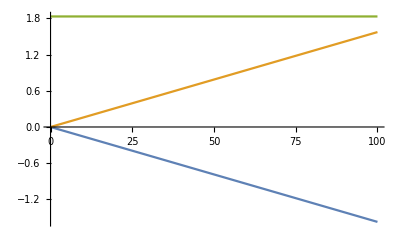

```mathematica
ClearAll;
xvec={x1[t],x2[t],x3[t]};
pvec={p1[t],p2[t],p3[t]};

(*spherical coordinates*)
radius=Sqrt[xvec.xvec];
theta=ArcCos[xvec[[3]]/radius];
phi=ArcTan[xvec[[1]],xvec[[2]]];

(*cylindrical coordinate*)
rho=CoordinateTransform["Cartesian"->"Cylindrical",xvec][[1]];
seta=CoordinateTransform["Cartesian"->"Cylindrical",xvec][[2]];
zd=CoordinateTransform["Cartesian"->"Cylindrical",xvec][[3]];

Prho=CoordinateTransform["Cartesian"->"Cylindrical",pvec][[1]];
Pseta=CoordinateTransform["Cartesian"->"Cylindrical",pvec][[2]];
Pz=CoordinateTransform["Cartesian"->"Cylindrical",pvec][[3]];


(*energy and orbital angular momentum as funcitons of x &p*)
L[{x1_,x2_,x3_},{p1_,p2_,p3_}]:=Sqrt[({x1,x2,x3}×{p1,p2,p3}).({x1,x2,x3}×{p1,p2,p3})];
En[{x1_,x2_,x3_},{p1_,p2_,p3_}]:=(-(Sqrt[rh]/(Sqrt[{x1,x2,x3}.{x1,x2,x3}])^(3/2) ){p1,p2,p3}.{x1,x2,x3})+c √({p1,p2,p3}.{p1,p2,p3});
 xinit= NSolve[L[{ a,-10,0},{0,1,0}]/En[{ a,-10,0},{0,1,0}]==1.5Sqrt[3]&& a>0, a];    (*calculating correct initial conditions for capturing or orbiting*)

rh=1;
c=1;

berry=2*((D[pvec, {t}])×pvec)/(2(√(pvec.pvec))^3);   (*berry phase term*)

(*H=(-(Sqrt[rh]/(radius)^(3/2) )pvec.xvec)+c √(pvec.pvec);*)
H=-(Sqrt[rh/rho] * pvec.{Cos[seta],Sin[seta],0})+c √(pvec.pvec);   

(*initial condisitons*)
init={x1[0]==5,x2[0]==-5rh,x3[0]==0,p1[0]==-2,p2[0]==10,p3[0]==0};     (*lengsing*)
cinit={x1[0]==4.8+0*3.3564456578574395,x2[0]==-5rh,x3[0]==0,p1[0]==-8,p2[0]==30,p3[0]==0};  (*capturing*)
binit={x1[0]==3rh/2,x2[0]==0,x3[0]==0,p1[0]==20,p2[0]==10Sqrt[2],p3[0]==0};    (*orbiting*)
cinit1={x1[0]==0.0,x2[0]==-1.45,x3[0]==0,p1[0]==100,p2[0]==-1.0,p3[0]==0};  (*capturing*)


(*eom*)
nob={D[xvec, {t}]==Hpvec,D[pvec, {t}]==-Hxvec,binit};
left={D[xvec, {t}]==berry+Hpvec,D[pvec, {t}]==-Hxvec,binit};
right={D[xvec, {t}]==-berry+Hpvec,D[pvec, {t}]==-Hxvec,binit};
left1={D[xvec, {t}]==berry+Hpvec,D[pvec, {t}]==-Hxvec,cinit1};

orb={D[xvec, {t}]==Hpvec,D[pvec, {t}]==-Hxvec,binit};
lefto={D[xvec, {t}]==berry+Hpvec,D[pvec, {t}]==-Hxvec,binit};
righto={D[xvec, {t}]==-berry+Hpvec,D[pvec, {t}]==-Hxvec,binit};


sol1=NDSolve[nob,{xvec[[1]],xvec[[2]],xvec[[3]],pvec[[1]],pvec[[2]],pvec[[3]] },{t,-30,40},WorkingPrecision->30];
(*sol2=NDSolve[cap,{xvec[[1]],xvec[[2]],xvec[[3]],pvec[[1]],pvec[[2]],pvec[[3]] },{t,0,5000},WorkingPrecision->60];*)
(*sol3=NDSolve[left,{xvec[[1]],xvec[[2]],xvec[[3]],pvec[[1]],pvec[[2]],pvec[[3]] },{t,0,5000},WorkingPrecision->50];*)sol4=NDSolve[left,{xvec[[1]],xvec[[2]],xvec[[3]],pvec[[1]],pvec[[2]],pvec[[3]] },{t,-30,40},WorkingPrecision->30];
sol5=NDSolve[right,{xvec[[1]],xvec[[2]],xvec[[3]],pvec[[1]],pvec[[2]],pvec[[3]] },{t,-30,40},WorkingPrecision->30];
sol6=NDSolve[left1,{xvec[[1]],xvec[[2]],xvec[[3]],pvec[[1]],pvec[[2]],pvec[[3]] },{t,-30,30},WorkingPrecision->30];



Show[ParametricPlot3D[{xvec/.sol1,xvec/.sol4,xvec/.sol5},{t,0,40},PlotStyle->{{Red,Thickness[0.02]},{Blue,Thickness[0.015]},{Orange,Thickness[0.015]}},AxesLabel->{x,y,z},Boxed-> False,Axes-> False],Graphics3D[{Opacity[0.2],Cylinder[{{0,0,-2},{0,0,2}},3rh/2]}],PlotRange->All]
(*,PlotLegends->{"Lensing","Capturing","Separatrix","Inner Capture"},Graphics3D[{Opacity[0.1],Cylinder[{{0,0,-5},{0,0,5}},3rh/2]},Boxed-> False],Graphics3D[Sphere[{3rh/2,0,-0},0.1],Boxed-> False],PlotRange->All]]*)
Plot[{rho/.sol1,rho/.sol4,rho/.sol5},{t,9,12},PlotStyle->{{Blue,Dashed},{Orange,Dotted},DotDashed},PlotRange->{0,5}]
Plot[{seta/.sol4,seta/.sol5},{t,0,100},PlotRange->{-5,5}]
Plot[{theta/.sol4,theta/.sol5},{t,0,100},PlotRange->{1,2}]
Plot[{xvec[[3]]/.sol4,xvec[[3]]/.sol5,1.83},{t,0,100}]
```

```mathematica
ParametricPlot[{xvec/.sol1,xvec[[2]]/.sol1},{t,0,20}]
```

-Graphics-

```mathematica
Plot[{pvec[[1]]/.sol1,pvec[[2]]/.sol1,pvec[[3]]/.sol1},{t,0,100},PlotRange-> All,PlotLabels->{"Px0","Py0","Pz0"}]
```

-Graphics-

```mathematica
Plot[{pvec[[1]]/.sol5,pvec[[2]]/.sol5,pvec[[3]]/.sol5},{t,0,100},PlotRange-> All,PlotLabels->{"PxR","PyR","PzR"}]
```

-Graphics-

```mathematica
Plot[{pvec[[1]]/.sol1,pvec[[1]]/.sol4,pvec[[1]]/.sol5,-1.2},{t,0,100},PlotRange-> All,PlotLabels->{"px0","pxL","pxR"}]
```

-Graphics-

```mathematica
Plot[{pvec[[2]]/.sol1,pvec[[2]]/.sol4,pvec[[2]]/.sol5,1},{t,0,100},PlotLabels->{"py0","pyL","pyR"},PlotRange-> {{0,100},{0,3}}]
```

-Graphics-

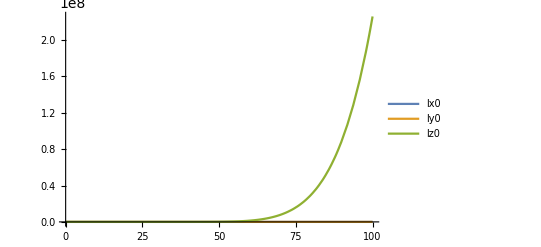
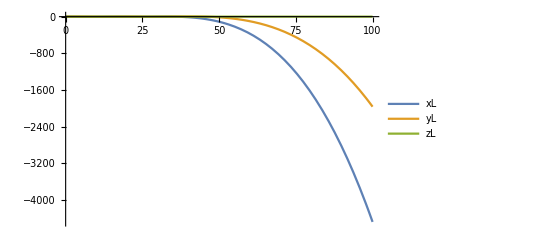

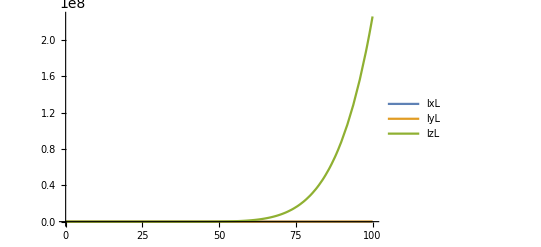

```mathematica
Plot[{xvec[[1]]/.sol1,xvec[[2]]/.sol1,xvec[[3]]/.sol1},{t,0,100},PlotLegends->{"xL","yL","zL"},PlotRange->All]Plot[{(xvec×pvec)[[1]]/.sol1,(xvec×pvec)[[2]]/.sol1,(xvec×pvec)[[3]]/.sol1},{t,0,100},PlotLegends->{"lx0","ly0","lz0"},PlotRange->All]
Plot[{(xvec×pvec)[[1]]/.sol4,(xvec×pvec)[[2]]/.sol4,(xvec×pvec)[[3]]/.sol4},{t,0,100},PlotLegends->{"lxL","lyL","lzL"},PlotRange->All](*orbital  angular momentum*)
```

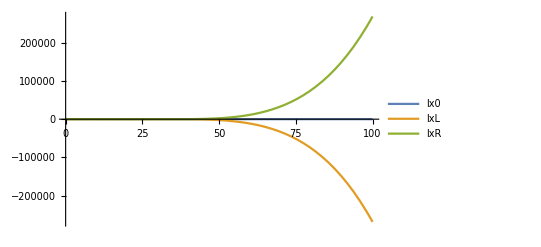

```mathematica
Plot[{(xvec×pvec)[[1]]/.sol1,(xvec×pvec)[[1]]/.sol4,(xvec×pvec)[[1]]/.sol5},{t,0,100},PlotLegends->{"lx0","lxL","lxR"},PlotRange->All]
```

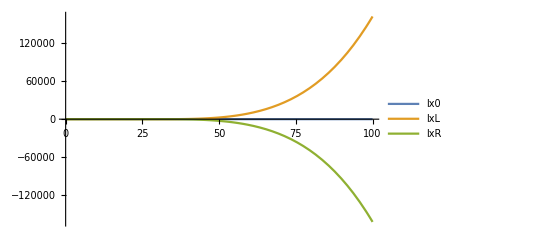

```mathematica
Plot[{(xvec×pvec)[[2]]/.sol1,(xvec×pvec)[[2]]/.sol4,(xvec×pvec)[[2]]/.sol5},{t,0,100},PlotLegends->{"lx0","lxL","lxR"},PlotRange->All]
```

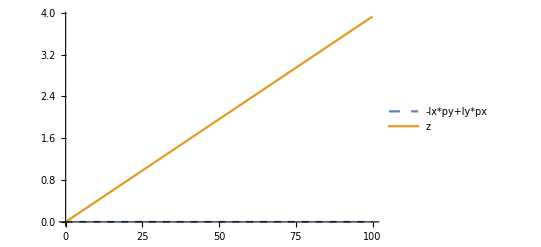

```mathematica
Plot[{-0*(((xvec×pvec)[[1]]*pvec[[2]]-((xvec×pvec)[[2]]*pvec[[1]]))/(pvec[[1]]^2+pvec[[2]]^2+pvec[[3]]^2))/.sol5,xvec[[3]]/.sol5},{t,0,100},PlotLegends->{"-lx*py+ly*px","z"},PlotRange->All,PlotStyle->{Dashed,Bold,Bold}]
```

```mathematica
Plot[{Prho/.sol1,Prho/.sol4,Prho/.sol5},{t,0,50},PlotRange-> {0,3}]
```

-Graphics-

```mathematica
FindMaximum[xvec[[3]]/.sol5 ,{t,60,80}]
```

InterpolatingFunction::dmval: Input value {60.} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {60.625} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {61.0113} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{712.745,{t→27200.3}}

```mathematica
Pi/0.82
```

3.83121

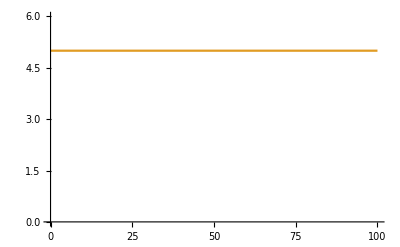

```mathematica
Plot[{(L[xvec,pvec]/.sol5-0*L[xvec,pvec]/.sol1),5},{t,0,100},PlotRange->{0,6}]
```

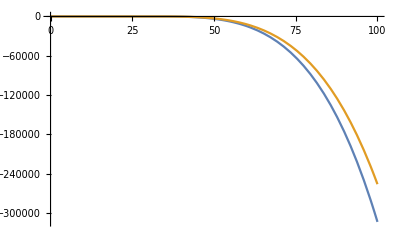

```mathematica
Plot[{xvec[[3]]*Prho/.sol4,((xvec×pvec).{-Sin[seta],Cos[seta],0})/.sol4},{t,0,100},PlotRange->All]
```

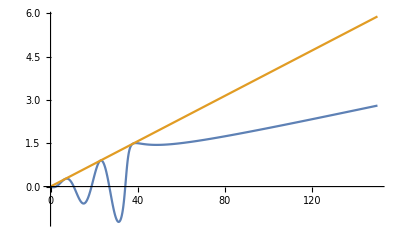

```mathematica
Plot[{(xvec×pvec)[[2]]/(Sqrt[pvec.pvec])/.sol4,-xvec[[3]]/.sol4},{t,0,150}]
```

```mathematica
(*orb=Table[
pos=Flatten[{r[t]Sin[θ[t]]Cos[ϕ[t]],r[t]Sin[θ[t]]Sin[ϕ[t]],r[t]Cos[θ[t]]}/.sols];
foo=Normalize@Flatten[{-r[t](kθ[t] Sin[ϕ[t]]+kϕ[t] Cos[θ[t]]Cos[ϕ[t]]),r[t](kθ[t] Cos[ϕ[t]]-kϕ[t] Cos[θ[t]]Sin[ϕ[t]]),r[t]Sin[θ[t]]kϕ[t]}/.sols];
{pos,pos+foo},{t,t1,t2,(t2-t1)/nt}];*)
```

```mathematica
{t1,t2}={0,25};
nt=50;
OrbAng=Table[
pos=Flatten[{xvec[[1]],xvec[[2]],xvec[[3]]}/.sol5];
Lo=Normalize@Flatten[{(xvec×pvec)[[1]],(xvec×pvec)[[2]],(xvec×pvec)[[3]]}/.sol5];
{pos,pos+Lo},{t,t1,t2,(t2-t1)/nt}];
```

```mathematica
SpinAng=Table[
pos=Flatten[{xvec[[1]],xvec[[2]],xvec[[3]]}/.sol5];
Sp=Normalize@Flatten[{pvec[[1]]/(pvec.pvec),pvec[[2]]/(pvec.pvec),pvec[[3]]/(pvec.pvec)}/.sol5];
{pos,pos+Sp},{t,t1,t2,(t2-t1)/nt}];
```

```mathematica
Show[ParametricPlot3D[{xvec/.sol1,xvec/.sol5},{t,t1,t2},PlotStyle->Thickness[0.006],Boxed->False,Axes-> False],Graphics3D[{Opacity[0.07],Orange,Cuboid[{-3,-3,-2},{3,3,3}]},Boxed-> False],Graphics3D[{Opacity[0.1],Green,Cylinder[{{0,0,3},{0,0,-2}},3rh/2]},Boxed-> False],Graphics3D[Sphere[{3rh/2,0,-0},0.1],Boxed-> False],Graphics3D[{Arrowheads[.01],Red,Arrow/@OrbAng},Boxed-> False],Graphics3D[{Arrowheads[.01],Blue,Arrow/@SpinAng},Boxed-> False],PlotRange->All]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

```mathematica
Sp1=Table[{{0,0,0},Normalize@Flatten[{(pvec)[[1]]/(pvec.pvec),(pvec)[[2]]/(pvec.pvec),(pvec)[[3]]/(pvec.pvec)}/.sol5]},{t,t1,t2,(t2-t1)/nt}];
Lo1=Table[{{0,0,0},Normalize@Flatten[{(xvec×pvec)[[1]],(xvec×pvec)[[2]],(xvec×pvec)[[3]]}/.sol5]},{t,t1,t2,(t2-t1)/nt}];
J1=Table[{{0,0,0},Normalize@Flatten[{(xvec×pvec)[[1]]+(pvec)[[1]]/(pvec.pvec),(xvec×pvec)[[2]]+(pvec)[[2]]/(pvec.pvec),(xvec×pvec)[[3]]+(pvec)[[3]]/(pvec.pvec)}/.sol5]},{t,t1,t2,(t2-t1)/nt}];
```

```mathematica
Graphics3D[{{Opacity[.05],Yellow,Sphere[{0,0,-0},1]},{Arrowheads[0.02],Thick,Red,Arrow/@J1},{Arrowheads[0.02],Thick,Green,Dashed,Arrow[{{0,0,0},{0,0,1.5}}]}},PlotLabel-> Style["Precession of Angular momentum",Bold,25],Boxed-> False]
Graphics3D[{{Opacity[.05],Blue,Sphere[{0,0,-0},1]},{Arrowheads[0.02],Blue,Thick,Arrow/@Sp1},{Arrowheads[0.02],Thick,Green,Dashed,Arrow[{{0,0,0},{0,0,1.5}}]}},PlotLabel->Style[ "Precession of Spin",Bold, 25],Boxed->False]
```

-Graphics3D-

-Graphics3D-